```mathematica
(*Calculamos una interpolación cualquiera con el soporte S={(1,1.2),(2,3),(3,2.1),(4,1),(5,0),(6,1.4)}*)
```

```mathematica
f=Interpolation[{1.2,3,2.1,1,0,1.4}]
```

InterpolatingFunction[{{1.,6.}},<>]

```mathematica
(*Escribimos la lista de imágenes de los puntos del soporte. Es decir, los f(xi) consistentes en las segundas coordenadas de los puntos de S*)
```

```mathematica
data={1.2,3,2.1,1,0,1.4}
```

{1.2,3,2.1,1,0,1.4}

```mathematica
(*Dibujamos el soporte (con sus imágenes) mediante puntos rojos y la interpolación que hemos determinado:*)
```

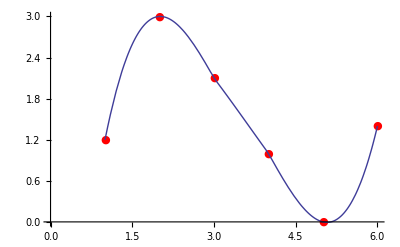

```mathematica
Show[ListPlot[data,PlotMarkers->{Automatic,Medium},PlotStyle->Red],Plot[f[x],{x,1,6}]]
```

```mathematica
(*La interpolación anterior corresponde a una función suficientemente diferenciable, si lo que queremos es la interpolación más simple que se puede realizar, solo tenemos que hacer la interpolación lineal:*)
```

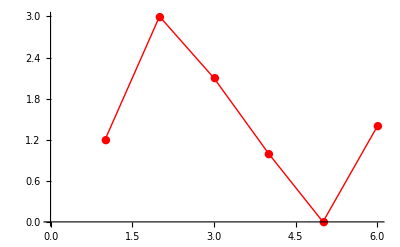

```mathematica
ListPlot[{data},PlotMarkers->{Automatic,Medium},PlotStyle->{Red},Joined->True]
```

```mathematica
(*Vamos a hacer una interpolación polinómica segmentada (ni de tipo Hermite ni cúbica porque el segundo punto del soporte es un punto "anguloso" (es decir, en el que no existe la derivada):*)
```

```mathematica
f[x_]:=Piecewise[{{x^3,1≤x≤2},{-x^4+x+22,2≤x≤3},{x^3+x-86,3≤x≤4}}]
```

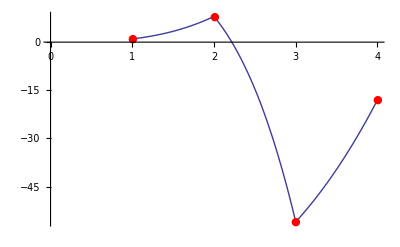

```mathematica
Show[ListPlot[{1,8,-56,-18},PlotMarkers->{Automatic,Medium},PlotStyle->{Red}],Plot[f[x],{x,1,4}]]
```

```mathematica
(*Estudiemos el error que se comete con un polinomio de interpolación Subscript[P, 3] para la siguiente función correspondiendo el soporte al intervalo [1,2]:*)
```

```mathematica
Clear[f]
f[x_]:=1/(1+9x^2)
```

```mathematica
f[x]
```

1/(1+9 x^2)

```mathematica
(*Calculamos la derivada primera:*)
```

```mathematica
f1[x_]:=f'[x]
```

```mathematica
f1[x]
```

-(18 x)/((1+9 x^2)^2)

```mathematica
(*Calculamos la derivada segunda:*)
```

```mathematica
f2[x_]:=f''[x]
```

```mathematica
f2[x]
```

(648 x^2)/((1+9 x^2)^3)-18/((1+9 x^2)^2)

```mathematica
Factor[f2[x]]
```

(18 (-1+27 x^2))/((1+9 x^2)^3)

```mathematica
(*Calculamos la derivada tercera:*)
```

```mathematica
f3[x_]:=f'''[x]
```

```mathematica
f3[x]
```

-(34992 x^3)/((1+9 x^2)^4)+(1944 x)/((1+9 x^2)^3)

```mathematica
Factor[f3[x]]
```

-(1944 x (-1+3 x) (1+3 x))/((1+9 x^2)^4)

```mathematica
(*Calculamos la derivada cuarta:*)
```

```mathematica
f4[x_]:=f3'[x]
```

```mathematica
f4[x]
```

(2519424 x^4)/((1+9 x^2)^5)-(209952 x^2)/((1+9 x^2)^4)+1944/((1+9 x^2)^3)

```mathematica
Factor[f4[x]]
```

(1944 (1-90 x^2+405 x^4))/((1+9 x^2)^5)

```mathematica
(*Como es el error cometido por el polinomio Subscript[P, 3], entonces hemos de considerar la derivada cuarta en valor absoluto en el intervalo [1,2]:*)
```

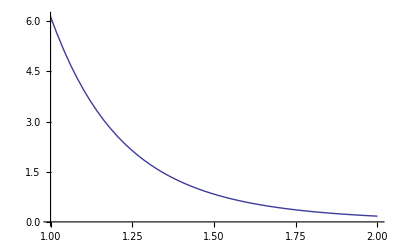

```mathematica
Plot[Abs[f4[x]],{x,1,2}]
```

```mathematica
(*El máximo se alcanza en x=1*)
```

```mathematica
f4[1]
```

19197/3125

```mathematica
N[%]
```

6.14304

```mathematica
(*La derivada en valor absoluto se divide por el factorial del orden de derivación, en este caso el orden de derivación es 4*)
```

```mathematica
4!
```

24

```mathematica
%%/%
```

0.25596

```mathematica
(*Que resulta ser el error que se comete, ya que la amplitud del intervalo [1,2] es 1, que sería por lo que deberíamos multiplicar el resultado del cociente anterior.

Repetimos el cálculo del error pero para el polinomio Subscript[P, 4] en el mismo intervalo. Se calcula la derivada quinta:*)
```

```mathematica
f5[x_]:=f4'[x]
```

```mathematica
f5[x]
```

-(226748160 x^5)/((1+9 x^2)^6)+(25194240 x^3)/((1+9 x^2)^5)-(524880 x)/((1+9 x^2)^4)

```mathematica
Factor[f5[x]]
```

-(524880 x (-1+3 x^2) (-1+27 x^2))/((1+9 x^2)^6)

```mathematica
(*Se estudia el máximo de la derivada en valor absoluto dentro de ese intervalo:*)
```

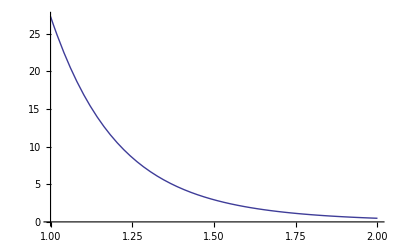

```mathematica
Plot[Abs[f5[x]],{x,1,2}]
```

```mathematica
(*El máximo se alcanza en x=1*)
```

```mathematica
f5[1]
```

-85293/3125

```mathematica
N[%]
```

-27.2938

```mathematica
(*El valor anterior debe dividirse por el factorial de orden de derivación y el cociente es el resultado del error, pues el intervalo es de amplitud 1:*)
```

```mathematica
5!
```

120

```mathematica
%%/%
```

-0.227448

```mathematica
(*Podemos calcular el error también para Subscript[P, 5]:*)
```

```mathematica
f6[x_]:=f5'[x]
```

```mathematica
f6[x]
```

(24488801280 x^6)/((1+9 x^2)^7)-(3401222400 x^4)/((1+9 x^2)^6)+(113374080 x^2)/((1+9 x^2)^5)-524880/((1+9 x^2)^4)

```mathematica
Factor[f6[x]]
```

(524880 (-1+189 x^2-2835 x^4+5103 x^6))/((1+9 x^2)^7)

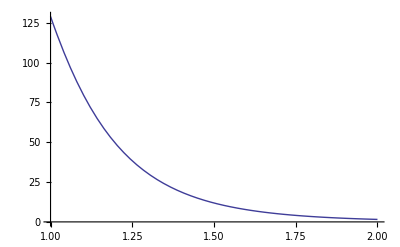

```mathematica
Plot[Abs[f6[x]],{x,1,2}]
```

```mathematica
f6[1]
```

2014227/15625

```mathematica
N[%]
```

128.911

```mathematica
6!
```

720

```mathematica
%%/%
```

0.179042

```mathematica
(*Cálculo de dos polinomios de interpolación para la f anterior para los dos soportes del intervalo [-1,1] que se indican a continuación:*)
```

```mathematica
S1=Table[-1+(i-1)2/(5),{i,1,6}]
S2=Table[-1+(i-1)2/(9),{i,1,10}]
```

{-1,-3/5,-1/5,1/5,3/5,1}

{-1,-7/9,-5/9,-1/3,-1/9,1/9,1/3,5/9,7/9,1}

```mathematica
(*Calculamos el polinomio para el soporte S1. Para dicho soporte, el sistema de ecuaciones resultante es:*)
({{1, S1[[1]], S1[[1]]^2, S1[[1]]^3, S1[[1]]^4, S1[[1]]^5}, {1, S1[[2]], S1[[2]]^2, S1[[2]]^3, S1[[2]]^4, S1[[2]]^5}, {1, S1[[3]], S1[[3]]^2, S1[[3]]^3, S1[[3]]^4, S1[[3]]^5}, {1, S1[[4]], S1[[4]]^2, S1[[4]]^3, S1[[4]]^4, S1[[4]]^5}, {1, S1[[5]], S1[[5]]^2, S1[[5]]^3, S1[[5]]^4, S1[[5]]^5}, {1, S1[[6]], S1[[6]]^2, S1[[6]]^3, S1[[6]]^4, S1[[6]]^5}}).({{a0}, {a1}, {a2}, {a3}, {a4}, {a5}})==({{f[S1[[1]]]}, {f[S1[[2]]]}, {f[S1[[3]]]}, {f[S1[[4]]]}, {f[S1[[5]]]}, {f[S1[[6]]]}})
```

{{a0-a1+a2-a3+a4-a5},{a0-(3 a1)/5+(9 a2)/25-(27 a3)/125+(81 a4)/625-(243 a5)/3125},{a0-a1/5+a2/25-a3/125+a4/625-a5/3125},{a0+a1/5+a2/25+a3/125+a4/625+a5/3125},{a0+(3 a1)/5+(9 a2)/25+(27 a3)/125+(81 a4)/625+(243 a5)/3125},{a0+a1+a2+a3+a4+a5}}=={{1/10},{25/106},{25/34},{25/34},{25/106},{1/10}}

```mathematica
(*Cuya solución resulta:*)
```

```mathematica
Solve[%]
```

{{a0→29479/36040,a1→0,a2→-225/106,a3→0,a4→10125/7208,a5→0}}

```mathematica
(*Por tanto, se obtiene el siguiente polinomio:*)
```

```mathematica
p5[x_]:=29479/36040-225/106 x^2+10125/7208 x^4
```

```mathematica
(*Para el soporte, repetimos todos los pasos anteriores pero con el sistema:*)
({{1, S2[[1]], S2[[1]]^2, S2[[1]]^3, S2[[1]]^4, S2[[1]]^5, S2[[1]]^6, S2[[1]]^7, S2[[1]]^8, S2[[1]]^9}, {1, S2[[2]], S2[[2]]^2, S2[[2]]^3, S2[[2]]^4, S2[[2]]^5, S2[[2]]^6, S2[[2]]^7, S2[[2]]^8, S2[[2]]^9}, {1, S2[[3]], S2[[3]]^2, S2[[3]]^3, S2[[3]]^4, S2[[3]]^5, S2[[3]]^6, S2[[3]]^7, S2[[3]]^8, S2[[3]]^9}, {1, S2[[4]], S2[[4]]^2, S2[[4]]^3, S2[[4]]^4, S2[[4]]^5, S2[[4]]^6, S2[[4]]^7, S2[[4]]^8, S2[[4]]^9}, {1, S2[[5]], S2[[5]]^2, S2[[5]]^3, S2[[5]]^4, S2[[5]]^5, S2[[5]]^6, S2[[5]]^7, S2[[5]]^8, S2[[5]]^9}, {1, S2[[6]], S2[[6]]^2, S2[[6]]^3, S2[[6]]^4, S2[[6]]^5, S2[[6]]^6, S2[[6]]^7, S2[[6]]^8, S2[[6]]^9}, {1, S2[[7]], S2[[7]]^2, S2[[7]]^3, S2[[7]]^4, S2[[7]]^5, S2[[7]]^6, S2[[7]]^7, S2[[7]]^8, S2[[7]]^9}, {1, S2[[8]], S2[[8]]^2, S2[[8]]^3, S2[[8]]^4, S2[[8]]^5, S2[[8]]^6, S2[[8]]^7, S2[[8]]^8, S2[[8]]^9}, {1, S2[[9]], S2[[9]]^2, S2[[9]]^3, S2[[9]]^4, S2[[9]]^5, S2[[9]]^6, S2[[9]]^7, S2[[9]]^8, S2[[9]]^9}, {1, S2[[10]], S2[[10]]^2, S2[[10]]^3, S2[[10]]^4, S2[[10]]^5, S2[[10]]^6, S2[[10]]^7, S2[[10]]^8, S2[[10]]^9}}).({{a0}, {a1}, {a2}, {a3}, {a4}, {a5}, {a6}, {a7}, {a8}, {a9}})==({{f[S2[[1]]]}, {f[S2[[2]]]}, {f[S2[[3]]]}, {f[S2[[4]]]}, {f[S2[[5]]]}, {f[S2[[6]]]}, {f[S2[[7]]]}, {f[S2[[8]]]}, {f[S2[[9]]]}, {f[S2[[10]]]}})
```

{{a0-a1+a2-a3+a4-a5+a6-a7+a8-a9},{a0-(7 a1)/9+(49 a2)/81-(343 a3)/729+(2401 a4)/6561-(16807 a5)/59049+(117649 a6)/531441-(823543 a7)/4782969+(5764801 a8)/43046721-(40353607 a9)/387420489},{a0-(5 a1)/9+(25 a2)/81-(125 a3)/729+(625 a4)/6561-(3125 a5)/59049+(15625 a6)/531441-(78125 a7)/4782969+(390625 a8)/43046721-(1953125 a9)/387420489},{a0-a1/3+a2/9-a3/27+a4/81-a5/243+a6/729-a7/2187+a8/6561-a9/19683},{a0-a1/9+a2/81-a3/729+a4/6561-a5/59049+a6/531441-a7/4782969+a8/43046721-a9/387420489},{a0+a1/9+a2/81+a3/729+a4/6561+a5/59049+a6/531441+a7/4782969+a8/43046721+a9/387420489},{a0+a1/3+a2/9+a3/27+a4/81+a5/243+a6/729+a7/2187+a8/6561+a9/19683},{a0+(5 a1)/9+(25 a2)/81+(125 a3)/729+(625 a4)/6561+(3125 a5)/59049+(15625 a6)/531441+(78125 a7)/4782969+(390625 a8)/43046721+(1953125 a9)/387420489},{a0+(7 a1)/9+(49 a2)/81+(343 a3)/729+(2401 a4)/6561+(16807 a5)/59049+(117649 a6)/531441+(823543 a7)/4782969+(5764801 a8)/43046721+(40353607 a9)/387420489},{a0+a1+a2+a3+a4+a5+a6+a7+a8+a9}}=={{1/10},{9/58},{9/34},{1/2},{9/10},{9/10},{1/2},{9/34},{9/58},{1/10}}

```mathematica
Solve[%]
```

{{a0→15335/15776,a1→0,a2→-1196577/197200,a3→0,a4→942597/49300,a5→0,a6→-177147/6800,a7→0,a8→4782969/394400,a9→0}}

```mathematica
(*Con lo que le polinomio interpolador es:*)
```

```mathematica
p9[x_]:=15335/15776-1196577/197200 x^2+942597/49300 x^4-177147/6800 x^6+4782969/394400 x^8
```

```mathematica
(*Dibujamos en la misma gráfica tanto la función como los dos polinomios:*)
```

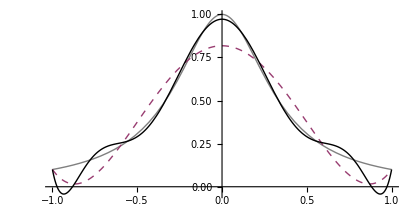

```mathematica
Plot[{f[x],p5[x],p9[x]},{x,-1,1},PlotStyle->{{Thick,Gray},Dashed,Black},AspectRatio->Automatic]
```

```mathematica
(*Y evaluamos el error absoluto que se comete al aproximar la función f por el primero de los polinomios:*)
```

```mathematica
Ea1[x_]:=Abs[f[x]-p5[x]]
```

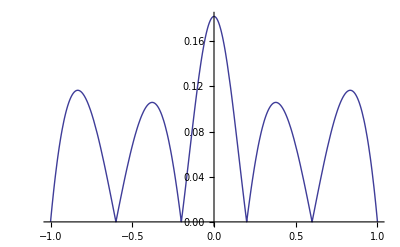

```mathematica
Plot[Ea1[x],{x,-1,1}]
```

```mathematica
(*Hacemos lo propio con el segundo polinomio:*)
```

```mathematica
Ea2[x_]:=Abs[f[x]-p9[x]]
```

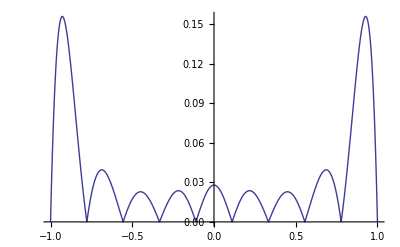

```mathematica
Plot[Ea2[x],{x,-1,1},PlotRange->Full]
```

```mathematica
(*¿Qué pasaría si el soporte no es equiespaciado y lo sesgo a uno de los extremos del intervalo [-1,1]? Veámoslo con un ejemplo dado por el soporte S3:*)
```

```mathematica
S3={-1,0,1/2,1}
```

{-1,0,1/2,1}

```mathematica
(*cuyo polinomio interpolador se calcula con el siguiente sistema lineal:)
```

```mathematica
({{1, S3[[1]], S3[[1]]^2, S3[[1]]^3}, {1, S3[[2]], S3[[2]]^2, S3[[2]]^3}, {1, S3[[3]], S3[[3]]^2, S3[[3]]^3}, {1, S3[[4]], S3[[4]]^2, S3[[4]]^3}}).({{a0}, {a1}, {a2}, {a3}})==({{f[S3[[1]]]}, {f[S3[[2]]]}, {f[S3[[3]]]}, {f[S3[[4]]]}})
```

{{a0-a1+a2-a3},{a0},{a0+a1/2+a2/4+a3/8},{a0+a1+a2+a3}}=={{1/10},{1},{4/13},{1/10}}

```mathematica
Solve[%]
```

{{a0→1,a1→-81/65,a2→-9/10,a3→81/65}}

```mathematica
(*siendo el polinomio:*)
```

```mathematica
p3[x_]:=1-81/65 x-9/10 x^2+81/65 x^3
```

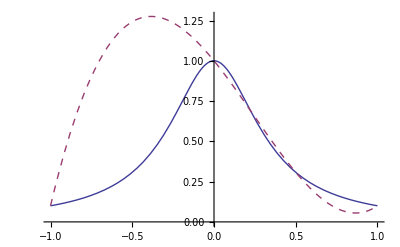

```mathematica
Plot[{f[x],p3[x]},{x,-1,1},PlotStyle->{Thick,Dashed}]
```

```mathematica
(*El error absoluto que se comete viene dado por la siguiente gráfica:*)
```

```mathematica
e3[x_]:=Abs[f[x]-p3[x]]
```

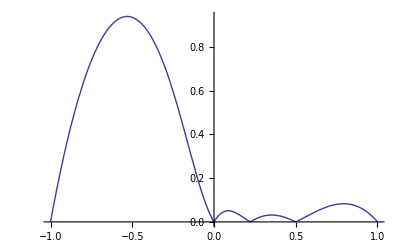

```mathematica
Plot[e3[x],{x,-1,1}]
```

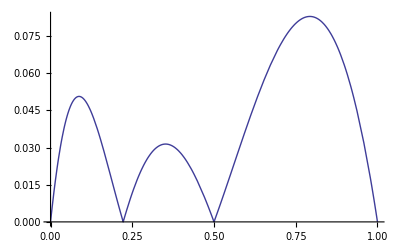

```mathematica
Plot[e3[x],{x,0,1}]
```

```mathematica
(*Calculemos el polinomio de Taylor de grado 3 en x=0 para la función f(x)=cos(x)*)
```

```mathematica
f[x_]:=Cos[x]
```

```mathematica
Series[f[x],{x,0,3}]
```

1-x^2/2+O[x]^4

```mathematica
(*Tomamos como polinomio interpolador a dicho polinomio:*)
```

```mathematica
p1[x_]:=1-x^2/2
```

```mathematica
(*Si tomamos el de grado 4:*)
```

```mathematica
Series[f[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
p2[x_]:=1-x^2/2+x^4/24
```

```mathematica
(*podemos dibujar ambos polinomios comparándolos con la gráfica que realmente corresponde a f*)
```

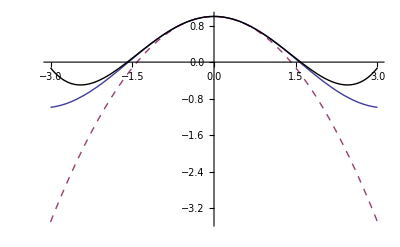

```mathematica
Plot[{f[x],p1[x],p2[x]},{x,-3,3},PlotStyle->{Thick,Dashed,Black}]
```

```mathematica
(*Los errores absolutos que cometemos para dichos polinomios aparecen en la siguiente gráfica:*)
```

```mathematica
ea1[x_]:=Abs[f[x]-p1[x]]
```

```mathematica
ea2[x_]:=Abs[f[x]-p2[x]]
```

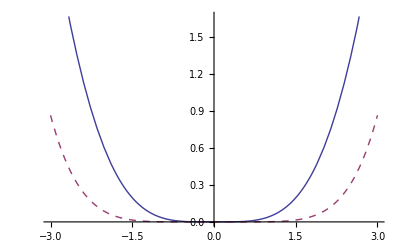

```mathematica
Plot[{ea1[x],ea2[x]},{x,-3,3},PlotStyle->{Thick,Dashed}]
```

```mathematica
(*Repetimos todo el proceso para la función g(x)=e^x y aproximamos con los polinomios de Taylor anteriores pero calculados para esta función:*)
```

```mathematica
g[x_]:=E^x
```

```mathematica
Series[g[x],{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

```mathematica
Series[g[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
p1[x_]:=1+x+x^2/2+x^3/6
```

```mathematica
p2[x_]:=1+x+x^2/2+x^3/6+x^4/24
```

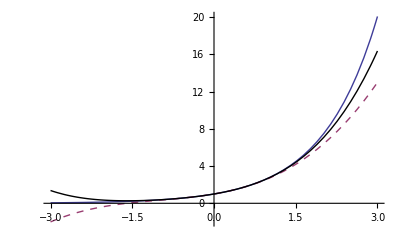

```mathematica
Plot[{g[x],p1[x],p2[x]},{x,-3,3},PlotStyle->{Thick,Dashed,Black}]
```

```mathematica
ea1[x_]:=Abs[g[x]-p1[x]]
```

```mathematica
ea2[x_]:=Abs[g[x]-p2[x]]
```

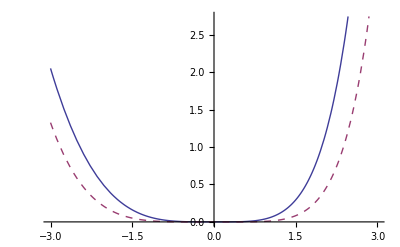

```mathematica
Plot[{ea1[x],ea2[x]},{x,-3,3},PlotStyle->{Thick,Dashed}]
```

```mathematica
(*Procedemos al cálculo del polinomio de interpolación de Hermite para el soporte S={Pi/4,Pi/3,Pi/2} con respecto de la función f(x)=cos(x). Primero damos estimaciones de los puntos del soporte:*)
```

```mathematica
Pi/4.
```

0.785398

```mathematica
Pi/3.`20
```

1.0471975511965977462

```mathematica
Pi/2.
```

1.5708

```mathematica
(*Introducimos la función y calculamos las imágenes por f para dichos puntos del soporte:*)
```

```mathematica
f[x_]:=Cos[x]
```

```mathematica
f[0.7854]
```

0.707105

```mathematica
f[1.047]
```

0.500171

```mathematica
f[1.571]
```

-0.000203673

```mathematica
(*Como es una interpolación de Hermite, debemos considerar que se toma un soporte auxiliar para realizar las diferencias divididas de Newton. El soporte auxiliar es {x0,x0,x1,x1,x2,x2}. Cuando calculemos las diferencias de primer orden, debemos tener en cuenta que si corresponde a considerar repetido el punto xi, entonces el resultado será la derivada f'(xi), mientras que si los dos puntos son distintos entonces sí será una diferencia dividida de Newton tal y como la hemos definido. De este modo, la primera diferencia corresponde a repetir el x0, por lo que el resultado será f'(x0)*)
```

```mathematica
d1=f'[0.7854]
```

-0.707108

```mathematica
(*La segunda de primer orden es considerando x0 y x1, por lo que se puee definir de la manera habitual y no considerar una derivada:*)
```

```mathematica
d2=(f[1.047]-f[0.7854])/(1.047-0.7854)
```

-0.791034

```mathematica
(*Y así sucesivamente*)
```

```mathematica
d3=f'[1.047]
```

-0.865927

```mathematica
d4=(f[1.571]-f[1.047])/(1.571-1.047)
```

-0.954914

```mathematica
d5=f'[1.571]
```

-1.

```mathematica
(*hasta haber calculado todas las posibles. Ahora debemos usar las diferencias anteriores para calcular las de segundo orden. Aquí ya no tenemos que preocuparnos por el que se pueda repetir algún xi. Esto ya no es posible*)
```

```mathematica
d12=(d2-d1)/(1.047-0.7854)
```

-0.320816

```mathematica
d23=(d3-d2)/(1.047-0.7854)
```

-0.286288

```mathematica
d34=(d4-d3)/(1.571-1.047)
```

-0.169823

```mathematica
d45=(d5-d4)/(1.571-1.047)
```

-0.0860426

```mathematica
(*Las de tercer orden:*)
```

```mathematica
d1223=(d23-d12)/(1.047-0.7854)
```

0.13199

```mathematica
d2334=(d34-d23)/(1.571-0.7854)
```

0.14825

```mathematica
d3445=(d45-d34)/(1.571-1.047)
```

0.159885

```mathematica
(*Las de cuarto*)
```

```mathematica
d122334=(d2334-d1223)/(1.571-0.7854)
```

0.0206985

```mathematica
d233445=(d3445-d2334)/(1.571-0.7854)
```

0.0148105

```mathematica
(*La de quinto*)
```

```mathematica
(d233445-d122334)/(1.571-0.7854)
```

-0.00749493

```mathematica
(*El polinomio interpolador corresponde a considerar la base de Newton de polinomios y como coordenada para el monomío de grado k la primera diferencia dividida de orden k que hemos calculado:)
```

```mathematica
0.707105-0.707108 (x-0.7854)-0.320816(x-0.7854)^2 + 0.13199 (x-0.7854)^2 (x-1.047)+0.0206985 (x-0.7854)^2 (x-1.047)^2-0.00749493(x-0.7854)^2 (x-1.047)^2 (x-1.571)
```

0.707105-0.707108 (-0.7854+x)-0.320816 (-0.7854+x)^2+0.13199 (-1.047+x) (-0.7854+x)^2+0.0206985 (-1.047+x)^2 (-0.7854+x)^2-0.00749493 (-1.571+x) (-1.047+x)^2 (-0.7854+x)^2

```mathematica
Expand[%]
```

1.00128-0.0076067 x-0.481312 x^2-0.0245092 x^3+0.0599405 x^4-0.00749493 x^5

```mathematica
(*Definimos el polinomio por si queremos hacer evaluaciones:*)
```

```mathematica
H5[x_]:=1.001284409971347-0.007606698654371469 x-0.48131215706190705 x^2-0.024509197228928803 x^3+0.059940454494 x^4-0.00749493 x^5
```

```mathematica
H5[x]
```

1.00128-0.0076067 x-0.481312 x^2-0.0245092 x^3+0.0599405 x^4-0.00749493 x^5

```mathematica
(*La gráfica del error absoluto que se comete con la aproximación es:*)
```

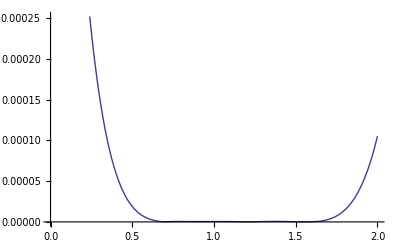

```mathematica
Plot[Abs[f[x]-H5[x]],{x,0,2}]
```

```mathematica
(*Si hacemos un "zoom":*)
```

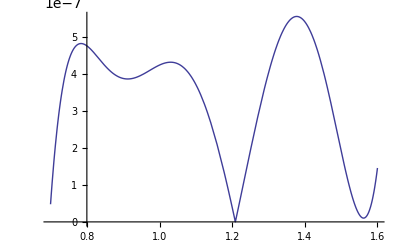

```mathematica
Plot[Abs[f[x]-H5[x]],{x,0.7,1.6}]
```

```mathematica
(*Y si volvemos a hacer un "zoom":*)
```

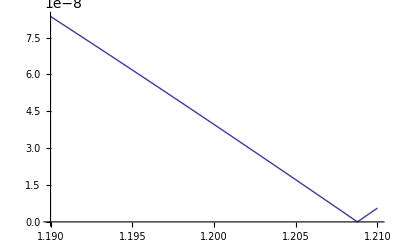

```mathematica
Plot[Abs[f[x]-H5[x]],{x,1.19,1.21}]
```

```mathematica
(*Esta sería la estimación del valor del polinomio para x=1.2*)
```

```mathematica
H5[1.2]
```

0.362358

```mathematica
(*Y esta sería una acotación del error absoluto que estaríamos comentiendo con dicha estimación:*)
```

```mathematica
1/720(1.2-0.7854)^2(1.2-1.047)^2(1.2-1.571)^2
```

7.69231×10^-7

```mathematica
(*Calculemos un spline cúbico con extremos libres. Primero indicamos los puntos del soporte. En este caso, el soporte tiene 7 puntos:*)
```

```mathematica
x0=0.8
x1=1.2
x2=1.7
x3=2.3
x4=2.5
x5=3.0
x6=4.1
```

0.8

1.2

1.7

2.3

2.5

3.

4.1

```mathematica
(*Ahora indicamos las imágenes de estos puntos por la función f a interpolar y que es nuestra incógnita:*)
```

```mathematica
y0=1.2
y1=1.4
y2=1.95
y3=2.23
y4=2
y5=2.4
y6=2.1
```

1.2

1.4

1.95

2.23

2

2.4

2.1

```mathematica
(*Seguidamente calculamos las amplitudes de los subintervalos que constituyen el soporte:*)
```

```mathematica
h0=x1-x0
h1=x2-x1
h2=x3-x2
h3=x4-x3
h4=x5-x4
h5=x6-x5
```

0.4

0.5

0.6

0.2

0.5

1.1

```mathematica
(*Ahora imponemos el sistema de ecuaciones lineales sobre las incógnitas ci que hemos de resolver para calcular parte del polinomio interpolador en el intervalo [Subscript[x, i],Subscript[x, i+1]]:*)
```

```mathematica
Clear[c0,c1,c2,c3,c4,c5,c6]
```

```mathematica
Solve[{c0==0,h0 c0+2(h0+h1) c1+h1 c2==3/h1(y2-y1)-3/h0(y1-y0),h1 c1+2(h1+h2)c2+h2 c3==3/h2(y3-y2)-3/h1(y2-y1),h2 c2+2(h2+h3)c3+h3 c4==3/h3(y4-y3)-3/h2(y3-y2),h3 c3+2(h3+h4)c4+h4 c5==3/h4(y5-y4)-3/h3(y4-y3),h4 c4+2(h4+h5)c5+h5 c6==3/h5(y6-y5)-3/h4(y5-y4),c6==0}]
```

{{c0→0.,c1→1.02711,c2→-0.0976084,c3→-3.6647,c4→5.3604,c5→-1.84324,c6→0.}}

```mathematica
(*Los valores de los coeficientes Subscript[c, i] son los siguientes y corresponden al coeficiente de grado 2 del spline cúbico:*)
```

```mathematica
c0=0
c1=1.02711
c2=-0.0976084
c3=-3.6647
c4=5.3604
c5=-1.84324
c6=0
```

0

1.02711

-0.0976084

-3.6647

5.3604

-1.84324

0

```mathematica
(*Los coeficientes de grado cero en el spline cúbico corresponden con las imágenes de f que hemos estimado:*)
```

```mathematica
a0=y0
a1=y1
a2=y2
a3=y3
a4=y4
a5=y5
```

1.2

1.4

1.95

2.23

2

2.4

```mathematica
(*Los coeficientes de grado 3 corresponde a los valores que se obtienen con las siguientes fórmulas:*)
```

```mathematica
d0=(c1-c0)/(3h0)
d1=(c2-c1)/(3h1)
d2=(c3-c2)/(3h2)
d3=(c4-c3)/(3h3)
d4=(c5-c4)/(3h4)
d5=(c6-c5)/(3h5)
```

0.855925

-0.749812

-1.98172

15.0418

-4.80243

0.558558

```mathematica
(*Finalmente, se calculan los coeficientes de grado 1 de cada polinomio en el spline:*)
```

```mathematica
b0=1/h0*(y1-y0)-h0/3*(2c0+c1)
b1=1/h1*(y2-y1)-h1/3*(2c1+c2)
b2=1/h2*(y3-y2)-h2/3*(2c2+c3)
b3=1/h3*(y4-y3)-h3/3*(2c3+c4)
b4=1/h4*(y5-y4)-h4/3*(2c4+c5)
b5=1/h5*(y6-y5)-h5/3*(2c5+c6)
```

0.363052

0.773898

1.23865

-1.01873

-0.679593

1.07898

```mathematica
(*Finalmente calculamos los 5 polinomios que corresponden a cada una de los trozos del spline cúbico. En concreto S0 es el polinomio para el intervalo [Subscript[x, 0],Subscript[x, 1]], el S1 al [Subscript[x, 1],Subscript[x, 2]] y así hasta S5 al [Subscript[x, 5],Subscript[x, 6]]:*)
```

```mathematica
S0[x_]:=a0+b0(x-x0)+c0(x-x0)^2+d0(x-x0)^3
S1[x_]:=a1+b1(x-x1)+c1(x-x1)^2+d1(x-x1)^3
S2[x_]:=a2+b2(x-x2)+c2(x-x2)^2+d2(x-x2)^3
S3[x_]:=a3+b3(x-x3)+c3(x-x3)^2+d3(x-x3)^3
S4[x_]:=a4+b4(x-x4)+c4(x-x4)^2+d4(x-x4)^3
S5[x_]:=a5+b5(x-x5)+c5(x-x5)^2+d5(x-x5)^3
```

```mathematica
Expand[S0[x]]
Expand[S1[x]]
Expand[S2[x]]
Expand[S3[x]]
Expand[S4[x]]
Expand[S5[x]]
```

0.471325+2.00643 x-2.05422 x^2+0.855925 x^3

3.24604-4.93035 x+3.72643 x^2-0.749812 x^3

9.29839-15.611 x+10.0092 x^2-1.98172 x^3

-197.827+254.553 x-107.453 x^2+15.0418 x^3

112.239-117.527 x+41.3786 x^2-4.80243 x^3

-32.5072+27.2195 x-6.87026 x^2+0.558558 x^3

```mathematica
(*Dibujamos la gráfica del spline cúbico que hemos determinado y vemos su comportamiento:*)
```

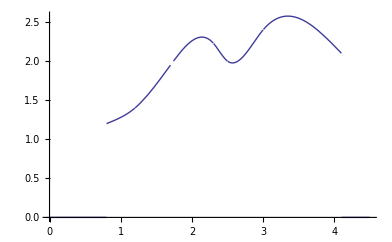

```mathematica
Plot[Piecewise[{{S0[x],0.8≤ x≤1.2},{S1[x],1.2≤ x≤1.7},{S2[x],1.7≤ x≤2.3},{S3[x],2.3≤ x≤2.5},{S4[x],2.5≤ x≤3.},{S5[x],3.≤ x≤4.1}}],{x,0,4.5}]
```